```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/autoindent.wl"];
Autoindent["model/model.wl"];
Autoindent["model/data.wl"];
Autoindent["model/gof-metrics.wl"];
```

```mathematica
SetDirectory[$UserDocumentsDirectory<>"/Github/covidmodel"];
Import["model/model.wl"]
```

Fitting model for CA

>> <|chiSquared→0.0000173696,rmsRelativeError→0.639546,rmsRelativeErrorDeaths→0.418543,rmsRelativeErrorPcr→0.781414,meanRelativeErrorDeaths→-0.31874,meanRelativeErrorPcr→-0.439378,rSquaredDeaths→0.0302398,rSquaredPcr→0.0377632,deathResidual7Day→1.54716,pcrResidual7Day→44.6842|>

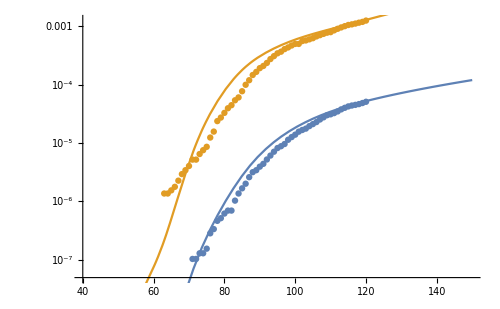
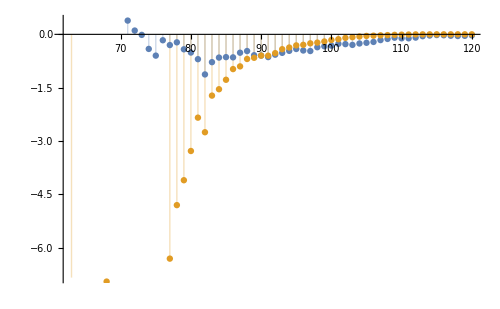
>> Fit for CA
-Graphics--Graphics-
 | Estimate | Standard Error | t-Statistic | P-Value
ⅇ^r0natural | 4.29902 | 2.52619 | 1.70178 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[1.70178,104.,HypothesisTesting`TwoSided→True]
ⅇ^importtime | 43.7962 | 19.9612 | 2.19406 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[2.19406,104.,HypothesisTesting`TwoSided→True]
ⅇ^stateAdjustmentForTestingDifferences | 0.59877 | 0.0270441 | 22.1405 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[22.1405,104.,HypothesisTesting`TwoSided→True]
ⅇ^distpow | 2.49148 | 1.14057 | 2.18442 | HypothesisTesting`TwoSidedPValue/.HypothesisTesting`StudentTPValue[2.18442,104.,HypothesisTesting`TwoSided→True] | DF | SS | MS
Model | 4 | 3.00757×10^-10 | 7.51892×10^-11
Error | 104 | 5.88996×10^-13 | 5.66342×10^-15
Uncorrected Total | 108 | 3.01346×10^-10 | 
Corrected Total | 107 | 7.49522×10^-11 |

>> <||>

>> <|containment→<|eventName→containment,day→591.187,thresholdCrossed→0.126846|>|>

>> Current Indefinite scenario Generating simulations for CA in the

>> <|herd→<|eventName→herd,day→255.539,thresholdCrossed→0.7|>,icu→<|eventName→icu,day→231.307,thresholdCrossed→0.00012435|>,hospital→<|eventName→hospital,day→238.94,thresholdCrossed→0.000952557|>|>

>> <|herd→<|eventName→herd,day→255.539,thresholdCrossed→0.7|>,icu→<|eventName→icu,day→231.307,thresholdCrossed→0.00012435|>,hospital→<|eventName→hospital,day→238.94,thresholdCrossed→0.000952557|>|>

>> Current scenario Generating simulations for CA in the

ParametricNDSolveValue::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t$1219925 = 217.803 and t$1219925 = 218.102.

>> <|herd→<|eventName→herd,day→312.725,thresholdCrossed→0.7|>,icu→<|eventName→icu,day→292.86,thresholdCrossed→0.00012435|>,hospital→<|eventName→hospital,day→296.984,thresholdCrossed→0.000952557|>|>

>> <|containment→<|eventName→containment,day→155.063,thresholdCrossed→0.0176083|>|>

>> Generating simulations for CA in the  Italy scenario

ParametricNDSolveValue::ndsz: At t$1220079 == 308.349, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {309} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

>> <|herd→<|eventName→herd,day→271.136,thresholdCrossed→0.7|>,icu→<|eventName→icu,day→251.273,thresholdCrossed→0.00012435|>,hospital→<|eventName→hospital,day→255.394,thresholdCrossed→0.000952557|>|>

>> <|containment→<|eventName→containment,day→146.462,thresholdCrossed→0.0171703|>|>

>> Generating simulations for CA in the  Wuhan scenario

>> <|herd→<|eventName→herd,day→166.497,thresholdCrossed→0.7|>,icu→<|eventName→icu,day→145.005,thresholdCrossed→0.00012435|>,hospital→<|eventName→hospital,day→150.145,thresholdCrossed→0.000952557|>|>

>> <|herd→<|eventName→herd,day→166.497,thresholdCrossed→0.7|>,icu→<|eventName→icu,day→145.005,thresholdCrossed→0.00012435|>,hospital→<|eventName→hospital,day→150.145,thresholdCrossed→0.000952557|>|>

>> Generating simulations for CA in the  Normal scenario

>> <|herd→<|eventName→herd,day→166.497,thresholdCrossed→0.7|>,icu→<|eventName→icu,day→145.005,thresholdCrossed→0.00012435|>,hospital→<|eventName→hospital,day→150.145,thresholdCrossed→0.000952557|>|>

>> <|herd→<|eventName→herd,day→166.497,thresholdCrossed→0.7|>,icu→<|eventName→icu,day→145.005,thresholdCrossed→0.00012435|>,hospital→<|eventName→hospital,day→150.145,thresholdCrossed→0.000952557|>|>

>> Generating simulations for CA in the  Open May 1 scenario

>> <|herd→<|eventName→herd,day→190.24,thresholdCrossed→0.7|>,icu→<|eventName→icu,day→160.476,thresholdCrossed→0.00012435|>,hospital→<|eventName→hospital,day→170.047,thresholdCrossed→0.000952557|>|>

>> <|herd→<|eventName→herd,day→190.24,thresholdCrossed→0.7|>,icu→<|eventName→icu,day→160.476,thresholdCrossed→0.00012435|>,hospital→<|eventName→hospital,day→170.047,thresholdCrossed→0.000952557|>|>

>> Generating simulations for CA in the  Open Gradual May 1 scenario

ParametricNDSolveValue::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t$1220695 = 142.358 and t$1220695 = 143.888.

>> <|icu→<|eventName→icu,day→164.547,thresholdCrossed→0.000150996|>|>

>> <|containment→<|eventName→containment,day→377.284,thresholdCrossed→0.353393|>,icu→<|eventName→icu,day→164.547,thresholdCrossed→0.000150996|>|>

>> Generating simulations for CA in the  relaxed restrictions scenario

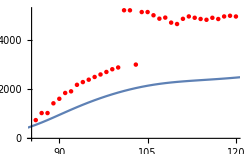
>> Current Hospitalizations for CA
-Graphics-Cumulative Hospitalizations for CA
-Graphics-Current ICU for CA
-Graphics-Cumulative ICU for CA
-Graphics-

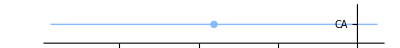
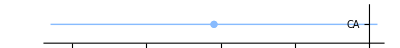
Currently Hospitalized
-Graphics- | Cumulative Hospitalized
-Graphics- | Currently ICU
-Graphics- | Cumulative ICU
-Graphics-

state | distancingLevel | id | distancingDays | maintain | name | gradual | summaryAug1 | totalProjectedDeaths | totalProjectedPCRConfirmed | totalProjectedInfected | totalInfectedFraction | fatalityRate | fatalityRateSymptomatic | fatalityRatePCR | fractionOfSymptomaticHospitalized | fractionOfSymptomaticHospitalizedOrICU | fractionOfPCRHospitalized | fractionOfPCRHospitalizedOrICU | fractionHospitalizedInICU | fractionOfDeathInICU | fractionDeathOfHospitalizedOrICU | fractionOfInfectionsPCRConfirmed | fractionOfDeathsReported | fractionOfHospitalizationsReported | dateContained | dateICUOverCapacity | dateHospitalsOverCapacity | {"r0natural", "importtime", "stateAdjustmentForTestingDifferences", "distpow"} |  |  |  | 
CA | 0.595037 | scenario5 | 608 | True | Current Indefinite | False | <|"totalProjectedDeaths" -> 17159.137945374023, "totalProjectedPCRConfirmed" -> 561553.0283730917, "totalProjectedInfected" -> 2.545208841123326*^6, "totalInfectedFraction" -> 0.06529048124995401, "fatalityRate" -> 0.006741740665100335, "fatalityRateSymptomatic" -> 0.009631058093000478, "fatalityRatePCR" -> 0.030556576277554356, "fractionOfSymptomaticHospitalized" -> 0.049774793413809776, "fractionOfSymptomaticHospitalizedOrICU" -> 0.06813170762899579, "fractionOfPCRHospitalized" -> 0.12118146390674114, "fractionOfPCRHospitalizedOrICU" -> 0.1658731157416943, "fractionHospitalizedInICU" -> 0.2694327627181562, "fractionOfDeathInICU" -> 0.6882621424254588, "fractionDeathOfHospitalizedOrICU" -> 0.16735819067953905, "fractionOfInfectionsPCRConfirmed" -> 0.2206314151121881, "fractionOfDeathsReported" -> 0.7687424807722502, "fractionOfHospitalizationsReported" -> 0.7673544904785639, "dateContained" -> "Fri 13 Aug 2021 04:29:30", "dateICUOverCapacity" -> "", "dateHospitalsOverCapacity" -> ""|> | 42385.3 | 1.27603×10^6 | 4.94482×10^6 | 0.126846 | 0.00857166 | 0.0122452 | 0.0332164 | 0.056861 | 0.0778313 | 0.118545 | 0.162264 | 0.269433 | 0.696183 | 0.167358 | 0.258055 | 0.769232 | 0.768569 | Fri 13 Aug 2021 04:29:30 |  |  | 4.29902 | 43.7962 | 0.59877 | 2.49148 | 
CA | 0.595037 | scenario1 | 90 | True | Current | False | <|"totalProjectedDeaths" -> 17159.15549970346, "totalProjectedPCRConfirmed" -> 561552.9881558196, "totalProjectedInfected" -> 2.5452086813125745*^6, "totalInfectedFraction" -> 0.06529047715043938, "fatalityRate" -> 0.00674174798541643, "fatalityRateSymptomatic" -> 0.009631068550594903, "fatalityRatePCR" -> 0.03055660972627954, "fractionOfSymptomaticHospitalized" -> 0.04977479727845042, "fractionOfSymptomaticHospitalizedOrICU" -> 0.06813171291891361, "fractionOfPCRHospitalized" -> 0.12118147439068125, "fractionOfPCRHospitalizedOrICU" -> 0.1658731300921053, "fractionHospitalizedInICU" -> 0.2694327627181562, "fractionOfDeathInICU" -> 0.688262725040809, "fractionDeathOfHospitalizedOrICU" -> 0.16735819067953905, "fractionOfInfectionsPCRConfirmed" -> 0.2206314131642143, "fractionOfDeathsReported" -> 0.7687424816130091, "fractionOfHospitalizationsReported" -> 0.7673544905113878, "dateContained" -> "", "dateICUOverCapacity" -> "Tue 18 Aug 2020 07:21:30", "dateHospitalsOverCapacity" -> "Tue 25 Aug 2020 22:32:58"|> | 237480. | 7.69264×10^6 | 2.76942×10^7 | 0.71042 | 0.00857507 | 0.0122501 | 0.030871 | 0.0568729 | 0.0778476 | 0.110271 | 0.150939 | 0.269433 | 0.696162 | 0.167358 | 0.277771 | 0.769505 | 0.769387 |  | Tue 18 Aug 2020 07:21:30 | Tue 25 Aug 2020 22:32:58 | 4.29902 | 43.7962 | 0.59877 | 2.49148 | 
CA | 0.2 | scenario2 | 90 | False | Italy | False | <|"totalProjectedDeaths" -> 5404.48393022423, "totalProjectedPCRConfirmed" -> 91542.75144342621, "totalProjectedInfected" -> 686421.631864386, "totalInfectedFraction" -> 0.01760829915435335, "fatalityRate" -> 0.00787341726912822, "fatalityRateSymptomatic" -> 0.011247738955897457, "fatalityRatePCR" -> 0.059037813972242496, "fractionOfSymptomaticHospitalized" -> 0.055570618579030354, "fractionOfSymptomaticHospitalizedOrICU" -> 0.07606502966898296, "fractionOfPCRHospitalized" -> 0.22232764747741587, "fractionOfPCRHospitalizedOrICU" -> 0.30432195167225196, "fractionHospitalizedInICU" -> 0.26943276271815636, "fractionOfDeathInICU" -> 0.6907943448651056, "fractionDeathOfHospitalizedOrICU" -> 0.1673581906795391, "fractionOfInfectionsPCRConfirmed" -> 0.13336227646962037, "fractionOfDeathsReported" -> 0.7669550106918137, "fractionOfHospitalizationsReported" -> 0.7622250222944753, "dateContained" -> "Wed 3 Jun 2020 01:30:54", "dateICUOverCapacity" -> "Sun 18 Oct 2020 20:37:41", "dateHospitalsOverCapacity" -> "Thu 22 Oct 2020 23:37:40"|> | 5404.48 | 91542.8 | 686422. | 0.0176083 | 0.00787342 | 0.0112477 | 0.0590378 | 0.0555706 | 0.076065 | 0.222328 | 0.304322 | 0.269433 | 0.690794 | 0.167358 | 0.133362 | 0.766955 | 0.762225 | Wed 3 Jun 2020 01:30:54 | Sun 18 Oct 2020 20:37:41 | Thu 22 Oct 2020 23:37:40 | 4.29902 | 43.7962 | 0.59877 | 2.49148 | 
CA | 0.11 | scenario3 | 60 | False | Wuhan | False | <|"totalProjectedDeaths" -> 4904.964069565114, "totalProjectedPCRConfirmed" -> 86816.06156434663, "totalProjectedInfected" -> 669346.2969102386, "totalInfectedFraction" -> 0.017170277402013212, "fatalityRate" -> 0.007327991642303633, "fatalityRateSymptomatic" -> 0.010468559489005191, "fatalityRatePCR" -> 0.05649834813031268, "fractionOfSymptomaticHospitalized" -> 0.054156506888056816, "fractionOfSymptomaticHospitalizedOrICU" -> 0.07412939442720166, "fractionOfPCRHospitalized" -> 0.222671154834219, "fractionOfPCRHospitalizedOrICU" -> 0.30479214433799645, "fractionHospitalizedInICU" -> 0.26943276271815625, "fractionOfDeathInICU" -> 0.6871417478334196, "fractionDeathOfHospitalizedOrICU" -> 0.16735819067953905, "fractionOfInfectionsPCRConfirmed" -> 0.1297027591922107, "fractionOfDeathsReported" -> 0.7666892802400337, "fractionOfHospitalizationsReported" -> 0.7618412643038505, "dateContained" -> "Mon 25 May 2020 11:04:37", "dateICUOverCapacity" -> "Mon 7 Sep 2020 06:33:41", "dateHospitalsOverCapacity" -> "Fri 11 Sep 2020 09:27:09"|> | 4904.96 | 86816.1 | 669346. | 0.0171703 | 0.00732799 | 0.0104686 | 0.0564983 | 0.0541565 | 0.0741294 | 0.222671 | 0.304792 | 0.269433 | 0.687142 | 0.167358 | 0.129703 | 0.766689 | 0.761841 | Mon 25 May 2020 11:04:37 | Mon 7 Sep 2020 06:33:41 | Fri 11 Sep 2020 09:27:09 | 4.29902 | 43.7962 | 0.59877 | 2.49148 | 
CA | 1 | scenario4 | 90 | False | Normal | False | <|"totalProjectedDeaths" -> 231608.70641416352, "totalProjectedPCRConfirmed" -> 7.546430172239496*^6, "totalProjectedInfected" -> 2.8309589454426255*^7, "totalInfectedFraction" -> 0.726206309519319, "fatalityRate" -> 0.008181281003280359, "fatalityRateSymptomatic" -> 0.011687544290400514, "fatalityRatePCR" -> 0.030691161400547454, "fractionOfSymptomaticHospitalized" -> 0.05610352777805789, "fractionOfSymptomaticHospitalizedOrICU" -> 0.07679447546374688, "fractionOfPCRHospitalized" -> 0.11335107919178039, "fractionOfPCRHospitalizedOrICU" -> 0.15515488979976116, "fractionHospitalizedInICU" -> 0.26943276271815625, "fractionOfDeathInICU" -> 0.6929589009605001, "fractionDeathOfHospitalizedOrICU" -> 0.16735819067953905, "fractionOfInfectionsPCRConfirmed" -> 0.26656798341735044, "fractionOfDeathsReported" -> 0.76950342610206, "fractionOfHospitalizationsReported" -> 0.769388047800921, "dateContained" -> "", "dateICUOverCapacity" -> "Sun 24 May 2020 00:07:13", "dateHospitalsOverCapacity" -> "Fri 29 May 2020 03:28:09"|> | 243374. | 7.59329×10^6 | 2.83815×10^7 | 0.728051 | 0.00857507 | 0.0122501 | 0.0320512 | 0.0568729 | 0.0778476 | 0.114487 | 0.15671 | 0.269433 | 0.696161 | 0.167358 | 0.267543 | 0.769506 | 0.769391 |  | Sun 24 May 2020 00:07:13 | Fri 29 May 2020 03:28:09 | 4.29902 | 43.7962 | 0.59877 | 2.49148 | 
CA | 0.595037 | scenario6 | 0 | True | 1 | Open May 1 | False | <|"totalProjectedDeaths" -> 231608.7064141634, "totalProjectedPCRConfirmed" -> 7.546430172239497*^6, "totalProjectedInfected" -> 2.8309589454426255*^7, "totalInfectedFraction" -> 0.726206309519319, "fatalityRate" -> 0.008181281003280355, "fatalityRateSymptomatic" -> 0.011687544290400509, "fatalityRatePCR" -> 0.030691161400547434, "fractionOfSymptomaticHospitalized" -> 0.056103527778057834, "fractionOfSymptomaticHospitalizedOrICU" -> 0.07679447546374678, "fractionOfPCRHospitalized" -> 0.11335107919178043, "fractionOfPCRHospitalizedOrICU" -> 0.15515488979976116, "fractionHospitalizedInICU" -> 0.2694327627181562, "fractionOfDeathInICU" -> 0.692958900960501, "fractionDeathOfHospitalizedOrICU" -> 0.16735819067953905, "fractionOfInfectionsPCRConfirmed" -> 0.26656798341735044, "fractionOfDeathsReported" -> 0.7695034261020596, "fractionOfHospitalizationsReported" -> 0.7693880478009221, "dateContained" -> "", "dateICUOverCapacity" -> "Sun 24 May 2020 00:07:13", "dateHospitalsOverCapacity" -> "Fri 29 May 2020 03:28:09"|> | 243374. | 7.59329×10^6 | 2.83815×10^7 | 0.728051 | 0.00857507 | 0.0122501 | 0.0320512 | 0.0568729 | 0.0778476 | 0.114487 | 0.15671 | 0.269433 | 0.696161 | 0.167358 | 0.267543 | 0.769506 | 0.769391 |  | Sun 24 May 2020 00:07:13 | Fri 29 May 2020 03:28:09 | 4.29902 | 43.7962 | 0.59877 | 2.49148
CA | 0.595037 | scenario7 | 60 | True | 1 | Open Gradual May 1 | True | <|"totalProjectedDeaths" -> 174425.0708860687, "totalProjectedPCRConfirmed" -> 7.145637099471085*^6, "totalProjectedInfected" -> 2.6733247041370194*^7, "totalInfectedFraction" -> 0.685769488343686, "fatalityRate" -> 0.006524649647539735, "fatalityRateSymptomatic" -> 0.009320928067913908, "fatalityRatePCR" -> 0.02441000969654329, "fractionOfSymptomaticHospitalized" -> 0.051099654165181176, "fractionOfSymptomaticHospitalizedOrICU" -> 0.06994517623771779, "fractionOfPCRHospitalized" -> 0.10295703027369109, "fractionOfPCRHospitalizedOrICU" -> 0.14092752182092658, "fractionHospitalizedInICU" -> 0.269432762718156, "fractionOfDeathInICU" -> 0.6820294829561886, "fractionDeathOfHospitalizedOrICU" -> 0.167358190679539, "fractionOfInfectionsPCRConfirmed" -> 0.26729402112706624, "fractionOfDeathsReported" -> 0.769483464904197, "fractionOfHospitalizationsReported" -> 0.7693593758747063, "dateContained" -> "", "dateICUOverCapacity" -> "Mon 8 Jun 2020 11:25:36", "dateHospitalsOverCapacity" -> "Thu 18 Jun 2020 01:07:57"|> | 236883. | 7.62594×10^6 | 2.76246×10^7 | 0.708634 | 0.00857507 | 0.0122501 | 0.0310628 | 0.0568729 | 0.0778476 | 0.110956 | 0.151876 | 0.269433 | 0.696162 | 0.167358 | 0.276056 | 0.769505 | 0.769386 |  | Mon 8 Jun 2020 11:25:36 | Thu 18 Jun 2020 01:07:57 | 4.29902 | 43.7962 | 0.59877 | 2.49148
CA | 0.7 | scenario8 | 608 | False | relaxed restrictions | False | <|"totalProjectedDeaths" -> 64790.61373036721, "totalProjectedPCRConfirmed" -> 2.742285810548798*^6, "totalProjectedInfected" -> 1.0960540815054681*^7, "totalInfectedFraction" -> 0.28116316940768027, "fatalityRate" -> 0.005911260659818452, "fatalityRateSymptomatic" -> 0.008444658085454932, "fatalityRatePCR" -> 0.02362649928068622, "fractionOfSymptomaticHospitalized" -> 0.04720671713180617, "fractionOfSymptomaticHospitalizedOrICU" -> 0.06461652634115374, "fractionOfPCRHospitalized" -> 0.10156885863514602, "fractionOfPCRHospitalizedOrICU" -> 0.1390273933074856, "fractionHospitalizedInICU" -> 0.2694327627181562, "fractionOfDeathInICU" -> 0.6815638088421707, "fractionDeathOfHospitalizedOrICU" -> 0.16735819067953905, "fractionOfInfectionsPCRConfirmed" -> 0.25019621356476995, "fractionOfDeathsReported" -> 0.7693466590461052, "fractionOfHospitalizationsReported" -> 0.7690232416850918, "dateContained" -> "Mon 11 Jan 2021 06:49:34", "dateICUOverCapacity" -> "Fri 12 Jun 2020 13:07:44", "dateHospitalsOverCapacity" -> ""|> | 118103. | 3.74072×10^6 | 1.37763×10^7 | 0.353393 | 0.00857292 | 0.012247 | 0.0315722 | 0.056867 | 0.0778395 | 0.112766 | 0.154354 | 0.269433 | 0.696156 | 0.167358 | 0.271534 | 0.769445 | 0.769207 | Mon 11 Jan 2021 06:49:34 | Fri 12 Jun 2020 13:07:44 |  | 4.29902 | 43.7962 | 0.59877 | 2.49148 |

```mathematica
asd=GenerateModelExport[100,{"CA"}];
TableForm[Import["tests/summary.csv"]]
```

```mathematica
100CDF[NormalDistribution[1,.05],0]
```

2.75362×10^-87